## Definition

```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=0.1;u0=10^-20;δstart=10^-10;m=10;αSch=2m;ee={10^-10,10^-5,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1};
Vs1[r_,a_,c1_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r];
Vs2[r_,a_,{c2_,d1_}]=- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r];V[r_]=-α/r;
```

```mathematica
RS[n_,r_]=2/(A^(3/2) n^(3/2)) ⅇ^(-r/(n A)) Hypergeometric1F1[1-n,2,(2 r)/(n A)]/.A->Rationalize@(1/(m α));
```

```mathematica
EigenEnergy[V_,αSch_]:=
Module[{min=1.*10^-19,max=5000,wpc=MachinePrecision,acg=30,sol,ef,evShifted,evnew,steps=∞,stepfraction=10^-2},
PrintTemporary[V];
Module[{shift=10,d=1000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->1}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
Print[evShifted];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u'[max]==-min,u[max]==min},u,{r,min,max},e,MaxSteps->steps,WorkingPrecision->wpc,AccuracyGoal->acg];
evnew=e/.#&/@
Table[
PrintTemporary[n];FindRoot[u[e][min]==0/.sol,{e,0.97 SetPrecision[evShifted[[n]],3],1.03 SetPrecision[evShifted[[n]],3]},WorkingPrecision->wpc,AccuracyGoal->acg,StepMonitor:>PrintTemporary[e]],{n,20}]
]
δ50e[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k,wpc=50,prc=20},
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},PrecisionGoal->prc,WorkingPrecision->wpc, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}(*,SolveDelayed->True*)];
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])/.sol,{δ,0},WorkingPrecision->wpc,PrecisionGoal->prc];
δr=δ/.δs;
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
]
δ50[V_]:=Module[{en,len,δen,timestampa,timestampb},
len=Length@ee;
ParallelTable[
timestampa=SessionTime[];
en=ee[[i]];
δen=δ50e[en,V];
timestampb=SessionTime[];
Print[{en,δen},"    ",timestampb-timestampa];
δen,{i,1,len}]
]
Eigenfun[V_,enelist_]:=Module[{},Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==# f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]]&/@enelist,2]]
```

```mathematica
Eigenfunsin[V_,ene_,rr_]:=
Module[{efunction,amplitude},efunction=Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==ene f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]],2];
amplitude=NIntegrate[f[r]^2/.#,{r,1.*10^-50,2000}]^-0.5&/@ef;
amplitude f[rr]/.efunction
]
```

```mathematica
δexpminus10=δ50e[10^-10,V[r]]
δexpminus5=δ50e[10^-5,V[r]]
δ50V=δ50[V[r]]
```

NDSolve::precw: 参数函数的精度 ({{20 (1/10000000000+0.1 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.000678812754891543949381320379508147712364611214578) 小于 WorkingPrecision (50.).

-0.00067881265062893030974528618332589351749288350356018

NDSolve::precw: 参数函数的精度 ({{20 (1/100000+0.1 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.217594907690330000572673776214958657314284704075) 小于 WorkingPrecision (50.).

-0.21425509081093643441231057599538933597199223090505

NDSolve::precw: The precision of the differential equation ({{20 (1/10000000000+0.1 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.003+0.1 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.03+0.1 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.3+0.1 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.508284) is less than WorkingPrecision (50.).

{0.003,0.47025305468871833275288953872430182006008095647764}    0.380268

NDSolve::precw: The precision of the differential equation ({{20 (0.007+0.1 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.595255) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000678812754891543949381320379508147712364611214578) is less than WorkingPrecision (50.).

{0.03,0.53692327081331265556478197935241031492051529710902}    0.599423

{1/10000000000,-0.00067881265062893030974528618332589351749288350356018}    0.601425

NDSolve::precw: The precision of the differential equation ({{20 (0.07+0.1 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (1/100000+0.1 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.249937) is less than WorkingPrecision (50.).

{0.007,0.24491924881014221725021613098865651587338166232147}    0.705499

NDSolve::precw: The precision of the differential equation ({{20 (0.01+0.1 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.217594907690330000572673776214958657314284704075) is less than WorkingPrecision (50.).

{1/100000,-0.21425509081093643441231057599538933597199223090505}    0.680481

NDSolve::precw: The precision of the differential equation ({{20 (0.001+0.1 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.406645) is less than WorkingPrecision (50.).

{0.07,0.38622193284258327679667570409297256098440426564577}    0.8015677

NDSolve::precw: The precision of the differential equation ({{20 (0.1+0.1 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-3.69987) is less than WorkingPrecision (50.).

{0.3,-1.306823869198648743887638863669500350119795836982}    1.622147

NDSolve::precw: The precision of the differential equation ({{20 (0.7+0.1 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.77006) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-1.0565465704809757376486563581289998556984731352562}    0.591418

FindRoot::precw: The precision of the argument function (Tan[δ]==0.489686) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.001,0.45536274512329869267537693226874707948371362013636}    0.7135062

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.908539) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,-0.7375128064744592799138625091349810048505849935441}    0.8846253

FindRoot::precw: The precision of the argument function (Tan[δ]==0.733685) is less than WorkingPrecision (50.).

{0.7,0.63297735444632006927971004451670400487064495081723}    2.200555

NDSolve::precw: The precision of the differential equation ({{20 (1+0.1 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==1.5311752167972842030940750123687404143221518337) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1,0.99224975307166676650317866616077929815025314430108}    2.20256

{-0.00067881265062893030974528618332589351749288350356018,-0.21425509081093643441231057599538933597199223090505,0.45536274512329869267537693226874707948371362013636,0.47025305468871833275288953872430182006008095647764,0.24491924881014221725021613098865651587338166232147,-1.0565465704809757376486563581289998556984731352562,0.53692327081331265556478197935241031492051529710902,0.38622193284258327679667570409297256098440426564577,-0.7375128064744592799138625091349810048505849935441,-1.306823869198648743887638863669500350119795836982,0.63297735444632006927971004451670400487064495081723,0.99224975307166676650317866616077929815025314430108}

## Determine the best 𝒶 value (using V_eff^(a^2))

```mathematica
aa={10,5,1,0.1,0.05,0.01,0.005,0.003};
```

```mathematica
hhhc1[en_,a_,c1_?NumberQ]:=δ50e[en,Vs1[r,a,c1]];
evnhhhc1[a_,c1_]:=N[hhhc1[10^-10,a,c1]-δexpminus10,8];
Determinec1[a_]:=Module[{aaa,findroot},aaa=a;
Print[aaa];findroot=FindRoot[hhhc1[10^-10,aaa,c1]==δexpminus10,{c1,-3.,-0.},MaxIterations->200,PrecisionGoal->20,WorkingPrecision->50,StepMonitor:>Print[{c1,evnhhhc1[aaa,c1]}]];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
c1a=Determinec1[#]&/@Drop[aa,0];
```

10

NDSolve::precw: 参数函数的精度 ({{20 (1/10000000000+0.0190481 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.00065575835460354348362304226582615352902164241929) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{20 (1.×10^-10+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.000848575427545171656444632801467589736890133983455) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{20 (1/10000000000+0.0190481 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.00065575835460354348362304226582615352902164241929) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

{-3.,0.00002305439}

{-2.6413,-0.000017238724}

{-2.79476,-1.6333043×10^-6}

{-2.80976,-2.0768597×10^-8}

{-2.80996,-1.7339147×10^-11}

{-2.80996,-1.7653309×10^-16}

{-2.809955621384211177371525991475,5.8373553×10^-21}

{-2.809955621384211123442601907279120786402723968509,-4.0604462×10^-33}

{-2.8099556213842111234426019073166335782646296847337,-9.34×10^-50}

-2.8099556213842111234426019073166335782646296855965

5

{0.08288850280884513185498147086671,-1.9491281×10^-6}

{0.06759994560699656279438606302989,-6.1105987×10^-8}

{0.0671051302175905060796749170862,3.9410585×10^-10}

{0.06710830110121343652914002098741,-8.1701309×10^-14}

{0.06710830044400002490839962124989,-1.0932035×10^-19}

{0.067108300443999145523514428604027613691093177604421,3.0271698×10^-29}

{0.06710830044399914552351467211288260501415476966558,-1.1211395×10^-44}

0.06710830044399914552351467211288260501415476966558

1

{-3.,0.000055218011}

{-1.71431,-9.2472327×10^-7}

{-1.73549,-1.9946307×10^-7}

{-1.74129,-4.0368762×10^-10}

{-1.7413,-1.7363096×10^-13}

{-1.7413,-1.5271397×10^-19}

{-1.7413010994999278402417530742241069674491882324219,8.0893272×10^-21}

{-1.741301099499927604502163768466048998618296165641,-2.6327356×10^-35}

{-1.7413010994999276045021637684668162317711110994866,-4.8×10^-51}

-1.7413010994999276045021637684668162317711110996265

0.1

{0.,-3.6628869×10^-6}

{-0.4994,-1.078998×10^-6}

{-0.696356,2.4817298×10^-8}

{-0.691928,-5.7192054×10^-10}

{-0.692027,-2.9652812×10^-13}

{-0.6920274738976316397653931744571,1.2255565×10^-21}

{-0.69202747389763142590464718920683343517036805237531,-2.7741191×10^-22}

{-0.69202747389763146537821106996607243178322770967848,-2.7741191×10^-22}

{-0.69202747389763146537821106996607243178322770967848,-2.7741191×10^-22}

{-0.69202747389763146537821106996607243178322770967848,-2.7741191×10^-22}

{-0.69202747389763147206230483343068430575663593372901,-2.7741191×10^-22}

{-0.69202747389763147206230483343068430575663593372901,-2.7741191×10^-22}

{-0.69202747389763147206230483343068430575663593372901,-2.7741191×10^-22}

{-0.69202747389763147273142900826379916238576048469008,-2.7741191×10^-22}

{-0.69202747389763147273142900826379916238576048469008,-2.7741191×10^-22}

{-0.69202747389763147297336023278421541626971039473201,-2.7741191×10^-22}

{-0.69202747389763147297336023278421541626971039473201,-2.7741191×10^-22}

{-0.69202747389763147306083385815807985236753663701248,-2.7741191×10^-22}

{-0.69202747389763147317506469137220491902482718425793,-2.7741191×10^-22}

{-0.69202747389763147317506469137220491902482718425793,-2.7741191×10^-22}

{-0.69202747389763147319087834905780363926691799012749,-2.7741191×10^-22}

{-0.69202747389763147321152922851853554581019522400407,-2.7741191×10^-22}

{-0.69202747389763147322185466824890149908183384094236,-2.7741191×10^-22}

{-0.69202747389763147322701738811408447571765314941151,-2.7741191×10^-22}

{-0.69202747389763147322959874804667596403556280364608,-2.7741191×10^-22}

{-0.69202747389763147323088942801297170819451763076337,-2.7741191×10^-22}

{-0.69202747389763147323153476799611958027399504432201,-2.7741191×10^-22}

{-0.69202747389763147323185743798769351631373375110133,-2.7741191×10^-22}

{-0.69202747389763147323185743798769351631373375110133,-2.7741191×10^-22}

{-0.69202747389763147323190210712516361132667719415267,-2.7741191×10^-22}

{-0.69202747389763147323190210712516361132667719415267,-2.7741191×10^-22}

{-0.69202747389763147323191825787794295339088709228099,-2.7741191×10^-22}

{-0.69202747389763147323193934896613250061051362080141,-2.7741191×10^-22}

{-0.69202747389763147323193934896613250061051362080141,-2.7741191×10^-22}

{-0.69202747389763147323193934896613250061051362080141,-2.7741191×10^-22}

«2 more identical outputs»

{-0.69202747389763147323193941093662251022333577129996,-2.7741191×10^-22}

{-0.69202747389763147323193941093662251022333577129996,-2.7741191×10^-22}

{-0.69202747389763147323193943334292181318175983766229,-2.7741191×10^-22}

{-0.69202747389763147323193946260305854219791709555655,-2.7741191×10^-22}

{-0.69202747389763147323193947723312690670599572450369,-2.7741191×10^-22}

{-0.69202747389763147323193947723312690670599572450369,-2.7741191×10^-22}

{-0.69202747389763147323193947925845480219253574040563,-2.7741191×10^-22}

{-0.69202747389763147323193947925845480219253574040563,-2.7741191×10^-22}

{-0.69202747389763147323193947999074049181453132908528,-2.7741191×10^-22}

{-0.69202747389763147323193947999074049181453132908528,-2.7741191×10^-22}

{-0.69202747389763147323193948025550864734143743295296,-2.7741191×10^-22}

{-0.69202747389763147323193948060126643301842289617066,-2.7741191×10^-22}

{-0.69202747389763147323193948060126643301842289617066,-2.7741191×10^-22}

{-0.69202747389763147323193948064913175196061507710417,-2.7741191×10^-22}

{-0.69202747389763147323193948064913175196061507710417,-2.7741191×10^-22}

{-0.69202747389763147323193948066643812895205019713518,-2.7741191×10^-22}

{-0.69202747389763147323193948066643812895205019713518,-2.7741191×10^-22}

{-0.69202747389763147323193948067269549213668497279557,-2.7741191×10^-22}

{-0.69202747389763147323193948068086691303354637379204,-2.7741191×10^-22}

{-0.69202747389763147323193948068086691303354637379204,-2.7741191×10^-22}

{-0.69202747389763147323193948068199813171795964428917,-2.7741191×10^-22}

{-0.69202747389763147323193948068347537759996835928972,-2.7741191×10^-22}

{-0.69202747389763147323193948068347537759996835928972,-2.7741191×10^-22}

{-0.69202747389763147323193948068347537759996835928972,-2.7741191×10^-22}

{-0.69202747389763147323193948068353199902057897389126,-2.7741191×10^-22}

{-0.69202747389763147323193948068360594030318243206637,-2.7741191×10^-22}

{-0.69202747389763147323193948068364291094448416115393,-2.7741191×10^-22}

{-0.69202747389763147323193948068364291094448416115393,-2.7741191×10^-22}

{-0.69202747389763147323193948068364802901155513047101,-2.7741191×10^-22}

{-0.69202747389763147323193948068364802901155513047101,-2.7741191×10^-22}

{-0.69202747389763147323193948068364987952044455454462,-2.7741191×10^-22}

{-0.69202747389763147323193948068364987952044455454462,-2.7741191×10^-22}

{-0.69202747389763147323193948068364987952044455454462,-2.7741191×10^-22}

«3 more identical outputs»

{-0.69202747389763147323193948068364988345225268759014,-2.7741191×10^-22}

{-0.6920274738976314732319394806836498885867571414327,-2.7741191×10^-22}

{-0.6920274738976314732319394806836498885867571414327,-2.7741191×10^-22}

{-0.69202747389763147323193948068364988929755731274939,-2.7741191×10^-22}

{-0.69202747389763147323193948068364988929755731274939,-2.7741191×10^-22}

{-0.69202747389763147323193948068364988955455707797063,-2.7741191×10^-22}

{-0.69202747389763147323193948068364988989017020926116,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989005797677490642,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989005797677490642,-2.7741191×10^-22}

{-0.6920274738976314732319394806836498900812072417764,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989011154364975272,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989011154364975272,-2.7741191×10^-22}

{-0.6920274738976314732319394806836498901157433002118,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012122757697634,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012396971535862,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012396971535862,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012434932598111,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012434932598111,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012448657952267,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012466581739405,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012475543632974,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012475543632974,-2.7741191×10^-22}

{-0.6920274738976314732319394806836498901247678428152,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012478404430639,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012479214505199,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012479619542479,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012479619542479,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012479675614213,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012479748837666,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012479748837666,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012479758974426,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012479772211909,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012479778830651,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012479778830651,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012479779746923,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012479780943472,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012479781541747,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012479781840884,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012479781990453,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012479782065237,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012479782102629,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012479782102629,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012479782102629,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012479782104062,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012479782104062,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012479782104062,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012479782104206,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012479782104393,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012479782104487,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012479782104487,-2.7741191×10^-22}

{-0.69202747389763147323193948068364989012479782104487,-2.7741191×10^-22}

{-0.6920274738976314732319394806836498901247978210449,-2.7741191×10^-22}

FindRoot::brdig: 根已经被 50. 工作数位紧密包围，但是函数值超过了绝对容差 1.×10^-25.

-0.6920274738976314732319394806836498901247978210449

0.05

{0.,-1.0787872×10^-6}

{-0.566517,-1.5646234×10^-7}

{-0.659481,8.4650877×10^-10}

{-0.658981,-4.6763223×10^-12}

{-0.658984,-1.3901952×10^-16}

{-0.6589837584428257510893445214606,4.3400285×10^-22}

{-0.65898375844282549600972054446665112360413665621398,-1.221599×10^-23}

{-0.65898375844282550299295325516819252680451459576974,-1.221599×10^-23}

{-0.65898375844282562704114888831439077412441763724034,-1.221599×10^-23}

{-0.65898375844282568906524670488748989778436915797564,-1.221599×10^-23}

{-0.65898375844282568906524670488748989778436915797564,-1.221599×10^-23}

{-0.65898375844282568991425357962615959311779102255737,-1.221599×10^-23}

{-0.65898375844282568991425357962615959311779102255737,-1.221599×10^-23}

{-0.65898375844282569032713552311282293815491864922764,-1.221599×10^-23}

{-0.65898375844282569032713552311282293815491864922764,-1.221599×10^-23}

{-0.65898375844282569052792482686233214458049426679987,-1.221599×10^-23}

{-0.65898375844282569409468994330939668842049378831943,-1.221599×10^-23}

{-0.65898375844282569409468994330939668842049378831943,-1.221599×10^-23}

{-0.65898375844282569414351303322191903788851086130135,-1.221599×10^-23}

{-0.65898375844282569501079276737742399911450220519027,-1.221599×10^-23}

{-0.65898375844282569544443263445517647972749787713474,-1.221599×10^-23}

{-0.65898375844282569544443263445517647972749787713474,-1.221599×10^-23}

{-0.65898375844282569545036844394326547887106097498024,-1.221599×10^-23}

{-0.65898375844282569555581050596865909945252834404361,-1.221599×10^-23}

{-0.65898375844282569555581050596865909945252834404361,-1.221599×10^-23}

{-0.65898375844282569555725383265453730993781098136586,-1.221599×10^-23}

{-0.65898375844282569555725383265453730993781098136586,-1.221599×10^-23}

{-0.65898375844282569555795573925256690759515370408723,-1.221599×10^-23}

{-0.6589837584428256955704242120352567587178451045289,-1.221599×10^-23}

{-0.65898375844282569557665844842660168427919080474974,-1.221599×10^-23}

{-0.65898375844282569557665844842660168427919080474974,-1.221599×10^-23}

{-0.65898375844282569557674378476749697336416841861657,-1.221599×10^-23}

{-0.65898375844282569557674378476749697336416841861657,-1.221599×10^-23}

{-0.65898375844282569557678528482518464828291955357779,-1.221599×10^-23}

{-0.65898375844282569557752248026003510424746779515807,-1.221599×10^-23}

{-0.65898375844282569557789107797746033222974191594822,-1.221599×10^-23}

{-0.65898375844282569557807537683617294622087897634329,-1.221599×10^-23}

{-0.65898375844282569557816752626552925321644750654083,-1.221599×10^-23}

{-0.65898375844282569557816752626552925321644750654083,-1.221599×10^-23}

{-0.65898375844282569557816878763815345679126946783223,-1.221599×10^-23}

{-0.65898375844282569557819119430918043175275061973591,-1.221599×10^-23}

{-0.65898375844282569557819119430918043175275061973591,-1.221599×10^-23}

{-0.65898375844282569557819150101928846376951881320937,-1.221599×10^-23}

{-0.65898375844282569557819150101928846376951881320937,-1.221599×10^-23}

{-0.65898375844282569557819165017599055789887788722493,-1.221599×10^-23}

{-0.65898375844282569557819165017599055789887788722493,-1.221599×10^-23}

{-0.65898375844282569557819172271263410821338082002418,-1.221599×10^-23}

{-0.65898375844282569557819301123331249145678613293047,-1.221599×10^-23}

{-0.65898375844282569557819301123331249145678613293047,-1.221599×10^-23}

{-0.65898375844282569557819302887102029698647099491319,-1.221599×10^-23}

{-0.65898375844282569557819302887102029698647099491319,-1.221599×10^-23}

{-0.65898375844282569557819303744844327679276392980436,-1.221599×10^-23}

{-0.65898375844282569557819318981538963341262191097638,-1.221599×10^-23}

{-0.65898375844282569557819326599886281172255090156239,-1.221599×10^-23}

{-0.65898375844282569557819326599886281172255090156239,-1.221599×10^-23}

{-0.65898375844282569557819326704168801590587293385711,-1.221599×10^-23}

{-0.65898375844282569557819328556614370839169416535625,-1.221599×10^-23}

{-0.65898375844282569557819328556614370839169416535625,-1.221599×10^-23}

{-0.65898375844282569557819328581971273700092484681943,-1.221599×10^-23}

{-0.65898375844282569557819328581971273700092484681943,-1.221599×10^-23}

{-0.65898375844282569557819328594302631249161810817968,-1.221599×10^-23}

{-0.65898375844282569557819328813353422915469146107115,-1.221599×10^-23}

{-0.65898375844282569557819328922878818748622813751689,-1.221599×10^-23}

{-0.65898375844282569557819328977641516665199647573976,-1.221599×10^-23}

{-0.65898375844282569557819329005022865623488064485119,-1.221599×10^-23}

{-0.65898375844282569557819329018713540102632272940691,-1.221599×10^-23}

{-0.65898375844282569557819329018713540102632272940691,-1.221599×10^-23}

{-0.65898375844282569557819329018900942695524109365185,-1.221599×10^-23}

{-0.65898375844282569557819329018900942695524109365185,-1.221599×10^-23}

{-0.65898375844282569557819329018992078761756126627076,-1.221599×10^-23}

{-0.65898375844282569557819329018992078761756126627076,-1.221599×10^-23}

{-0.65898375844282569557819329019036399293505868767632,-1.221599×10^-23}

{-0.65898375844282569557819329019823696841908026857293,-1.221599×10^-23}

{-0.65898375844282569557819329020217345616109105902123,-1.221599×10^-23}

{-0.65898375844282569557819329020217345616109105902123,-1.221599×10^-23}

{-0.6589837584428256955781932902022273401396242967809,-1.221599×10^-23}

{-0.6589837584428256955781932902022273401396242967809,-1.221599×10^-23}

{-0.65898375844282569557819329020225354454672812012653,-1.221599×10^-23}

{-0.65898375844282569557819329020271903231629424781983,-1.221599×10^-23}

{-0.65898375844282569557819329020271903231629424781983,-1.221599×10^-23}

{-0.65898375844282569557819329020272540407066683318618,-1.221599×10^-23}

{-0.65898375844282569557819329020272540407066683318618,-1.221599×10^-23}

{-0.65898375844282569557819329020272850272911948996196,-1.221599×10^-23}

{-0.65898375844282569557819329020272850272911948996196,-1.221599×10^-23}

{-0.65898375844282569557819329020273000964285859025936,-1.221599×10^-23}

{-0.65898375844282569557819329020275677803767718572675,-1.221599×10^-23}

{-0.65898375844282569557819329020275677803767718572675,-1.221599×10^-23}

{-0.65898375844282569557819329020275714445253893699123,-1.221599×10^-23}

{-0.65898375844282569557819329020275714445253893699123,-1.221599×10^-23}

{-0.65898375844282569557819329020275732264435898417997,-1.221599×10^-23}

{-0.6589837584428256955781932902027604879940858472029,-1.221599×10^-23}

{-0.6589837584428256955781932902027604879940858472029,-1.221599×10^-23}

{-0.65898375844282569557819329020276053132246584245035,-1.221599×10^-23}

{-0.65898375844282569557819329020276130099570756058236,-1.221599×10^-23}

{-0.65898375844282569557819329020276168583232841964836,-1.221599×10^-23}

{-0.65898375844282569557819329020276187825063884918137,-1.221599×10^-23}

{-0.65898375844282569557819329020276197445979406394787,-1.221599×10^-23}

{-0.65898375844282569557819329020276197445979406394787,-1.221599×10^-23}

{-0.6589837584428256955781932902027619757767375917957,-1.221599×10^-23}

{-0.65898375844282569557819329020276199917055463156341,-1.221599×10^-23}

{-0.65898375844282569557819329020276199917055463156341,-1.221599×10^-23}

{-0.65898375844282569557819329020276199949077712882373,-1.221599×10^-23}

{-0.65898375844282569557819329020276199949077712882373,-1.221599×10^-23}

{-0.65898375844282569557819329020276199964650506336806,-1.221599×10^-23}

{-0.65898375844282569557819329020276199964650506336806,-1.221599×10^-23}

{-0.6589837584428256955781932902027619997222373738863,-1.221599×10^-23}

{-0.6589837584428256955781932902027619997222373738863,-1.221599×10^-23}

{-0.65898375844282569557819329020276199975906687960866,-1.221599×10^-23}

{-0.65898375844282569557819329020276199975906687960866,-1.221599×10^-23}

{-0.65898375844282569557819329020276199977697749771169,-1.221599×10^-23}

{-0.65898375844282569557819329020276200009513671571277,-1.221599×10^-23}

{-0.65898375844282569557819329020276200025421632471331,-1.221599×10^-23}

{-0.65898375844282569557819329020276200025421632471331,-1.221599×10^-23}

{-0.65898375844282569557819329020276200025639386032329,-1.221599×10^-23}

{-0.65898375844282569557819329020276200025639386032329,-1.221599×10^-23}

{-0.65898375844282569557819329020276200025745282128274,-1.221599×10^-23}

{-0.65898375844282569557819329020276200025745282128274,-1.221599×10^-23}

{-0.65898375844282569557819329020276200025796780634591,-1.221599×10^-23}

{-0.65898375844282569557819329020276200025796780634591,-1.221599×10^-23}

{-0.65898375844282569557819329020276200025821824958739,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026266705338657,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026266705338657,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026272795012095,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026272795012095,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026272795012095,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026272876087557,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026272876087557,-1.221599×10^-23}

{-0.658983758442825695578193290202762000262729155155,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273615902464,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273615902464,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273625489598,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273625489598,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273630151933,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273712972353,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273712972353,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273714106027,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273714106027,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273714657346,-1.221599×10^-23}

{-0.6589837584428256955781932902027620002627372445082,-1.221599×10^-23}

{-0.6589837584428256955781932902027620002627372445082,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273724584877,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273726966217,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273726966217,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273726998814,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273726998814,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273727014666,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273727296258,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273727296258,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273727300113,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273727368583,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273727402819,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273727402819,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273727403287,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273727411612,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273727415774,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273727415774,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273727415831,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273727416843,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273727416843,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273727416857,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273727416857,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273727416864,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273727416984,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273727416984,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273727416985,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273727416985,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273727416986,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273727416986,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273727416989,-1.221599×10^-23}

{-0.65898375844282569557819329020276200026273727416989,-1.221599×10^-23}

FindRoot::brdig: 根已经被 50. 工作数位紧密包围，但是函数值超过了绝对容差 1.×10^-25.

-0.65898375844282569557819329020276200026273727416991

0.01

{0.,-4.9150911×10^-8}

{-0.618956,-1.1942752×10^-9}

{-0.634273,1.7976972×10^-13}

{-0.634271,-2.8081291×10^-17}

{-0.6342706750303552798442296989379,9.8383369×10^-24}

{-0.63427067503035527984422969893785193562507629394531,9.8383369×10^-24}

{-0.63427067503035527984422969893785193562507629394531,9.8383369×10^-24}

{-0.63427067503035525339759450360161100445204834085858,9.8383369×10^-24}

{-0.63427067503035523774155100850128208600033567497776,9.8383369×10^-24}

{-0.63427067503035522991352926095111762677447934203735,9.8383369×10^-24}

{-0.63427067503035522599951838717603539716155117556715,9.8383369×10^-24}

{-0.63427067503035522599951838717603539716155117556715,9.8383369×10^-24}

{-0.63427067503035522510344231578374859954415324380262,9.8383369×10^-24}

{-0.63427067503035522457297763303612144094962016806733,9.8383369×10^-24}

{-0.63427067503035522457297763303612144094962016806733,9.8383369×10^-24}

{-0.634270675030355224451532720321715773336992229657,9.8383369×10^-24}

{-0.63427067503035522437963900599201181749467292992835,9.8383369×10^-24}

{-0.63427067503035522434369214882715983957351328006402,9.8383369×10^-24}

{-0.63427067503035522434369214882715983957351328006402,9.8383369×10^-24}

{-0.63427067503035522433546245310428810951231222464425,9.8383369×10^-24}

{-0.63427067503035522433546245310428810951231222464425,9.8383369×10^-24}

{-0.63427067503035522433323171687409871809024794259417,9.8383369×10^-24}

{-0.63427067503035522433323171687409871809024794259417,9.8383369×10^-24}

{-0.63427067503035522433323171687409871809024794259417,9.8383369×10^-24}

«1 more identical outputs»

{-0.63427067503035522433310494632852277946380210792543,9.8383369×10^-24}

{-0.63427067503035522433310494632852277946380210792543,9.8383369×10^-24}

{-0.63427067503035522433310494632852277946380210792543,9.8383369×10^-24}

{-0.63427067503035522433308921245517522967977957979223,9.8383369×10^-24}

{-0.63427067503035522433307989821902926134176864340544,9.8383369×10^-24}

{-0.63427067503035522433307989821902926134176864340544,9.8383369×10^-24}

{-0.63427067503035522433307989821902926134176864340544,9.8383369×10^-24}

{-0.63427067503035522433307892182987911586832785388161,9.8383369×10^-24}

{-0.63427067503035522433307892182987911586832785388161,9.8383369×10^-24}

{-0.63427067503035522433307865717044025713654500311604,9.8383369×10^-24}

{-0.63427067503035522433307850049570051966536052457219,9.8383369×10^-24}

{-0.63427067503035522433307850049570051966536052457219,9.8383369×10^-24}

{-0.63427067503035522433307850049570051966536052457219,9.8383369×10^-24}

{-0.63427067503035522433307848407186140026015902244862,9.8383369×10^-24}

{-0.63427067503035522433307847434917502784472274778508,9.8383369×10^-24}

{-0.63427067503035522433307846948783184163700461045331,9.8383369×10^-24}

{-0.63427067503035522433307846948783184163700461045331,9.8383369×10^-24}

{-0.63427067503035522433307846837487292443676628347073,9.8383369×10^-24}

{-0.63427067503035522433307846771601658648495591262908,9.8383369×10^-24}

{-0.63427067503035522433307846771601658648495591262908,9.8383369×10^-24}

{-0.63427067503035522433307846771601658648495591262908,9.8383369×10^-24}

«1 more identical outputs»

{-0.6342706750303552243330784676843924062641726109706,9.8383369×10^-24}

{-0.6342706750303552243330784676843924062641726109706,9.8383369×10^-24}

{-0.6342706750303552243330784676843924062641726109706,9.8383369×10^-24}

{-0.63427067503035522433307846768046743422864692610856,9.8383369×10^-24}

{-0.63427067503035522433307846768046743422864692610856,9.8383369×10^-24}

{-0.63427067503035522433307846768046743422864692610856,9.8383369×10^-24}

«1 more identical outputs»

{-0.63427067503035522433307846768024438192888145843505,9.8383369×10^-24}

{-0.63427067503035522433307846768011233804197420682119,9.8383369×10^-24}

{-0.63427067503035522433307846768004631609852058101426,9.8383369×10^-24}

{-0.63427067503035522433307846768004631609852058101426,9.8383369×10^-24}

{-0.63427067503035522433307846768003120099393259913218,9.8383369×10^-24}

{-0.63427067503035522433307846768003120099393259913218,9.8383369×10^-24}

{-0.63427067503035522433307846768002710390303605413343,9.8383369×10^-24}

{-0.63427067503035522433307846768002710390303605413343,9.8383369×10^-24}

{-0.63427067503035522433307846768002599334811287492621,9.8383369×10^-24}

{-0.63427067503035522433307846768002533591490624690183,9.8383369×10^-24}

{-0.63427067503035522433307846768002500719830293288964,9.8383369×10^-24}

{-0.63427067503035522433307846768002500719830293288964,9.8383369×10^-24}

{-0.63427067503035522433307846768002493194172036368052,9.8383369×10^-24}

{-0.63427067503035522433307846768002493194172036368052,9.8383369×10^-24}

{-0.63427067503035522433307846768002493194172036368052,9.8383369×10^-24}

{-0.63427067503035522433307846768002492260139976054746,9.8383369×10^-24}

{-0.63427067503035522433307846768002491707205871051397,9.8383369×10^-24}

{-0.63427067503035522433307846768002491707205871051397,9.8383369×10^-24}

{-0.63427067503035522433307846768002491580616794901916,9.8383369×10^-24}

{-0.63427067503035522433307846768002491505677806725819,9.8383369×10^-24}

{-0.63427067503035522433307846768002491468208312637771,9.8383369×10^-24}

{-0.63427067503035522433307846768002491449473565593747,9.8383369×10^-24}

{-0.63427067503035522433307846768002491449473565593747,9.8383369×10^-24}

{-0.63427067503035522433307846768002491445184421012617,9.8383369×10^-24}

{-0.63427067503035522433307846768002491445184421012617,9.8383369×10^-24}

{-0.63427067503035522433307846768002491445184421012617,9.8383369×10^-24}

{-0.6342706750303552243330784676800249144465208239009,9.8383369×10^-24}

{-0.6342706750303552243330784676800249144465208239009,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444507787012474,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444422366137893,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444379655700603,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444358300481958,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444358300481958,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444353411404987,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444350517138811,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444350517138811,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444349854523722,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444349462264722,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444349462264722,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444349372460704,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444349319297963,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444349292716593,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444349292716593,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444349292716593,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444349289930131,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444349289930131,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444349289174835,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444349289174835,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444349288970105,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444349288970105,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444349288970105,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444349288944695,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444349288944695,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444349288944695,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444349288941541,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444349288941541,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444349288940686,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444349288940686,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444349288940455,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444349288940455,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444349288940455,9.8383369×10^-24}

«1 more identical outputs»

{-0.63427067503035522433307846768002491444349288940442,9.8383369×10^-24}

{-0.63427067503035522433307846768002491444349288940434,9.8383369×10^-24}

FindRoot::brdig: 根已经被 50. 工作数位紧密包围，但是函数值超过了绝对容差 1.×10^-25.

General::stop: 在本次计算中，FindRoot::brdig 的进一步输出将被抑制.

-0.6342706750303552243330784676800249144434928894043

0.005

{0.,-1.2481156×10^-8}

{-0.62402,-1.440359×10^-10}

{-0.631284,4.8749639×10^-15}

{-0.6312835806409957672968857878004,-1.7192375×10^-19}

{-0.6312835806496649180403568863673,-2.2191388×10^-24}

{-0.631283580649665029940529711336,-6.6852669×10^-24}

{-0.631283580649665029940529711336,-6.6852669×10^-24}

{-0.63128358064966536704105679923199009328724788540485,4.8904603×10^-25}

{-0.63128358064966534406217725644348698223368612398478,4.8904603×10^-25}

{-0.63128358064966534406217725644348698223368612398478,4.8904603×10^-25}

{-0.63128358064966534406217725644348698223368612398478,4.8904603×10^-25}

{-0.6312835806496653347030132343032441927409120506382,4.8904603×10^-25}

{-0.6312835806496653347030132343032441927409120506382,4.8904603×10^-25}

{-0.6312835806496653347030132343032441927409120506382,4.8904603×10^-25}

{-0.63128358064966533383953663590131607603607160668059,4.8904603×10^-25}

{-0.63128358064966533250264902707686410327859483551177,4.8904603×10^-25}

{-0.63128358064966533250264902707686410327859483551177,4.8904603×10^-25}

{-0.63128358064966533250264902707686410327859483551177,4.8904603×10^-25}

{-0.63128358064966533246281684579315242128678989378998,4.8904603×10^-25}

{-0.63128358064966533240114621141904488072748861711981,4.8904603×10^-25}

{-0.63128358064966533237031089423199111044783797878472,4.8904603×10^-25}

{-0.63128358064966533237031089423199111044783797878472,4.8904603×10^-25}

{-0.63128358064966533236654729805903785901052672495379,4.8904603×10^-25}

{-0.63128358064966533236654729805903785901052672495379,4.8904603×10^-25}

{-0.63128358064966533236512486467009758298784469222966,4.8904603×10^-25}

{-0.63128358064966533236292256575942431257355719225757,4.8904603×10^-25}

{-0.63128358064966533236292256575942431257355719225757,4.8904603×10^-25}

{-0.63128358064966533236292256575942431257355719225757,4.8904603×10^-25}

{-0.63128358064966533236285694889763890471894676652945,4.8904603×10^-25}

{-0.63128358064966533236275535683409808625610689884187,4.8904603×10^-25}

{-0.63128358064966533236275535683409808625610689884187,4.8904603×10^-25}

{-0.63128358064966533236274295704267628183045591675215,4.8904603×10^-25}

{-0.63128358064966533236274295704267628183045591675215,4.8904603×10^-25}

{-0.63128358064966533236273827060010281370261840484063,4.8904603×10^-25}

{-0.63128358064966533236273101476130239656509492285787,4.8904603×10^-25}

{-0.63128358064966533236273101476130239656509492285787,4.8904603×10^-25}

{-0.63128358064966533236273012915188981426312172425272,4.8904603×10^-25}

{-0.63128358064966533236273012915188981426312172425272,4.8904603×10^-25}

{-0.63128358064966533236273012915188981426312172425272,4.8904603×10^-25}

{-0.63128358064966533236273004744555351325400349347756,4.8904603×10^-25}

{-0.63128358064966533236273004744555351325400349347756,4.8904603×10^-25}

{-0.6312835806496653323627300165650298062324965164838,4.8904603×10^-25}

{-0.6312835806496653323627299687539025859553030448376,4.8904603×10^-25}

{-0.6312835806496653323627299448483389758167063090145,4.8904603×10^-25}

{-0.6312835806496653323627299448483389758167063090145,4.8904603×10^-25}

{-0.63128358064966533236272994193055197302295924975891,4.8904603×10^-25}

{-0.63128358064966533236272994193055197302295924975891,4.8904603×10^-25}

{-0.63128358064966533236272994193055197302295924975891,4.8904603×10^-25}

{-0.63128358064966533236272994166135690495131762914652,4.8904603×10^-25}

{-0.63128358064966533236272994166135690495131762914652,4.8904603×10^-25}

{-0.63128358064966533236272994155961590103731728117109,4.8904603×10^-25}

{-0.63128358064966533236272994155961590103731728117109,4.8904603×10^-25}

{-0.63128358064966533236272994152116336937847636792878,4.8904603×10^-25}

{-0.63128358064966533236272994146162879345855578409104,4.8904603×10^-25}

{-0.63128358064966533236272994146162879345855578409104,4.8904603×10^-25}

{-0.63128358064966533236272994145436231714078722941541,4.8904603×10^-25}

{-0.63128358064966533236272994145436231714078722941541,4.8904603×10^-25}

{-0.63128358064966533236272994145161598675374488658211,4.8904603×10^-25}

{-0.63128358064966533236272994145161598675374488658211,4.8904603×10^-25}

{-0.63128358064966533236272994145161598675374488658211,4.8904603×10^-25}

{-0.63128358064966533236272994145136261027534560261583,4.8904603×10^-25}

{-0.63128358064966533236272994145136261027534560261583,4.8904603×10^-25}

{-0.63128358064966533236272994145126684783264855959998,4.8904603×10^-25}

{-0.63128358064966533236272994145111858252555236607319,4.8904603×10^-25}

{-0.63128358064966533236272994145111858252555236607319,4.8904603×10^-25}

{-0.63128358064966533236272994145111858252555236607319,4.8904603×10^-25}

{-0.63128358064966533236272994145111416500342757521358,4.8904603×10^-25}

{-0.63128358064966533236272994145110732552381542273059,4.8904603×10^-25}

{-0.63128358064966533236272994145110732552381542273059,4.8904603×10^-25}

{-0.63128358064966533236272994145110732552381542273059,4.8904603×10^-25}

«1 more identical outputs»

{-0.63128358064966533236272994145110727577911211915665,4.8904603×10^-25}

{-0.63128358064966533236272994145110719876130112777973,4.8904603×10^-25}

{-0.63128358064966533236272994145110716025239563209126,4.8904603×10^-25}

{-0.63128358064966533236272994145110716025239563209126,4.8904603×10^-25}

{-0.6312835806496653323627299414511071555522017450298,4.8904603×10^-25}

{-0.6312835806496653323627299414511071555522017450298,4.8904603×10^-25}

{-0.63128358064966533236272994145110715377578567587352,4.8904603×10^-25}

{-0.63128358064966533236272994145110715377578567587352,4.8904603×10^-25}

{-0.63128358064966533236272994145110715310439761687379,4.8904603×10^-25}

{-0.63128358064966533236272994145110715206491330606488,4.8904603×10^-25}

{-0.63128358064966533236272994145110715206491330606488,4.8904603×10^-25}

{-0.63128358064966533236272994145110715193803933391557,4.8904603×10^-25}

{-0.63128358064966533236272994145110715193803933391557,4.8904603×10^-25}

{-0.63128358064966533236272994145110715189008791567639,4.8904603×10^-25}

{-0.63128358064966533236272994145110715181584657898219,4.8904603×10^-25}

{-0.63128358064966533236272994145110715181584657898219,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180678507301609,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180678507301609,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180678507301609,4.8904603×10^-25}

«1 more identical outputs»

{-0.63128358064966533236272994145110715180658099393599,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180658099393599,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180650386321203,4.8904603×10^-25}

{-0.6312835806496653323627299414511071518063844446785,4.8904603×10^-25}

{-0.6312835806496653323627299414511071518063844446785,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180636986908217,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180636986908217,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180636436030442,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180635583127569,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180635583127569,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180635479026743,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180635479026743,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180635479026743,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180635469422399,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180635454552363,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180635454552363,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180635452737405,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180635452737405,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180635452737405,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180635452569957,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180635452310704,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180635452310704,4.8904603×10^-25}

{-0.6312835806496653323627299414511071518063545227906,4.8904603×10^-25}

{-0.6312835806496653323627299414511071518063545227906,4.8904603×10^-25}

{-0.6312835806496653323627299414511071518063545227906,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180635452276141,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180635452271621,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180635452271621,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180635452271069,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180635452271069,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180635452270861,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180635452270538,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180635452270538,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180635452270538,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180635452270528,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180635452270514,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180635452270514,4.8904603×10^-25}

{-0.63128358064966533236272994145110715180635452270512,4.8904603×10^-25}

-0.63128358064966533236272994145110715180635452270509

0.003

{0.,-4.5209936×10^-9}

{-0.625852,-3.0501043×10^-11}

{-0.630095,3.5212325×10^-16}

{-0.6300949257771031319919075031066,-4.250225×10^-21}

{-0.6300949257776944312041752293161,-1.3788312×10^-24}

{-0.63009492577769462309199279276021162591511127160156,3.61785×10^-25}

{-0.63009492577769458320834016737217318069718516032709,1.2561182×10^-25}

{-0.63009492577769456376682043383719597603151060658695,1.2561182×10^-25}

{-0.63009492577769449748549783157663458411752582815459,1.2561182×10^-25}

{-0.63009492577769449748549783157663458411752582815459,1.2561182×10^-25}

{-0.63009492577769449471845478478340642699503057608352,1.2561182×10^-25}

{-0.63009492577769449471845478478340642699503057608352,1.2561182×10^-25}

{-0.63009492577769449345044886853229039115188324520772,1.2561182×10^-25}

{-0.63009492577769449345044886853229039115188324520772,1.2561182×10^-25}

{-0.63009492577769449286938128972783939257224927946213,1.2561182×10^-25}

{-0.63009492577769449286938128972783939257224927946213,1.2561182×10^-25}

{-0.63009492577769449260310529936345319026424100402119,1.2561182×10^-25}

{-0.63009492577769449260310529936345319026424100402119,1.2561182×10^-25}

{-0.63009492577769449248108351458169386959460245012821,1.2561182×10^-25}

{-0.63009492577769449248108351458169386959460245012821,1.2561182×10^-25}

{-0.63009492577769449242516665951357203074108000078701,1.2561182×10^-25}

{-0.63009492577769449242516665951357203074108000078701,1.2561182×10^-25}

{-0.6300949257776944923995425901205406364929493003899,1.2561182×10^-25}

{-0.6300949257776944923995425901205406364929493003899,1.2561182×10^-25}

{-0.63009492577769449238780028216243067707653569218999,1.2561182×10^-25}

{-0.63009492577769449232335307745453304097045226057798,1.2561182×10^-25}

{-0.63009492577769449229112947510058422291741054477198,1.2561182×10^-25}

{-0.63009492577769449229112947510058422291741054477198,1.2561182×10^-25}

{-0.63009492577769449228978423799101147300261344416955,1.2561182×10^-25}

{-0.63009492577769449228978423799101147300261344416955,1.2561182×10^-25}

{-0.63009492577769449228916777898229614379007635765618,1.2561182×10^-25}

{-0.63009492577769449228916777898229614379007635765618,1.2561182×10^-25}

{-0.63009492577769449228888528476122385860903327488335,1.2561182×10^-25}

{-0.63009492577769449228733482611551362611372361823554,1.2561182×10^-25}

{-0.63009492577769449228655959679265850986606878991163,1.2561182×10^-25}

{-0.63009492577769449228617198213123095174224137574968,1.2561182×10^-25}

{-0.6300949257776944922859781748005171726803276686687,1.2561182×10^-25}

{-0.6300949257776944922859781748005171726803276686687,1.2561182×10^-25}

{-0.6300949257776944922859781748005171726803276686687,1.2561182×10^-25}

{-0.63009492577769449228597749926265529280976879554224,1.2561182×10^-25}

{-0.63009492577769449228597749926265529280976879554224,1.2561182×10^-25}

{-0.63009492577769449228597718969536955505560003317898,1.2561182×10^-25}

{-0.63009492577769449228597549064725175892235147955573,1.2561182×10^-25}

{-0.63009492577769449228597464112319286085572720274411,1.2561182×10^-25}

{-0.63009492577769449228597421636116341182241506433829,1.2561182×10^-25}

{-0.63009492577769449228597421636116341182241506433829,1.2561182×10^-25}

{-0.63009492577769449228597419862864429506232507310951,1.2561182×10^-25}

{-0.63009492577769449228597410130439649118404203412245,1.2561182×10^-25}

{-0.63009492577769449228597410130439649118404203412245,1.2561182×10^-25}

{-0.63009492577769449228597409724140600461644494738894,1.2561182×10^-25}

{-0.63009492577769449228597409724140600461644494738894,1.2561182×10^-25}

{-0.63009492577769449228597409537952822117887575042812,1.2561182×10^-25}

{-0.63009492577769449228597409537952822117887575042812,1.2561182×10^-25}

{-0.63009492577769449228597409452631704780323727114374,1.2561182×10^-25}

{-0.63009492577769449228597409452631704780323727114374,1.2561182×10^-25}

{-0.63009492577769449228597409413533042513190905233298,1.2561182×10^-25}

{-0.63009492577769449228597409413533042513190905233298,1.2561182×10^-25}

{-0.63009492577769449228597409395615961270206744500843,1.2561182×10^-25}

{-0.63009492577769449228597409297278751349126242457024,1.2561182×10^-25}

{-0.63009492577769449228597409297278751349126242457024,1.2561182×10^-25}

{-0.63009492577769449228597409293173472783911075468772,1.2561182×10^-25}

{-0.63009492577769449228597409293173472783911075468772,1.2561182×10^-25}

{-0.63009492577769449228597409291292216359445801983212,1.2561182×10^-25}

{-0.63009492577769449228597409280967012972847167717578,1.2561182×10^-25}

{-0.6300949257776944922859740927580441127954785058476,1.2561182×10^-25}

{-0.6300949257776944922859740927580441127954785058476,1.2561182×10^-25}

{-0.63009492577769449228597409275588888405863980875608,1.2561182×10^-25}

{-0.6300949257776944922859740927440599941938108644698,1.2561182×10^-25}

{-0.63009492577769449228597409273814554926139639232666,1.2561182×10^-25}

{-0.63009492577769449228597409273814554926139639232666,1.2561182×10^-25}

{-0.63009492577769449228597409273789863922575807580801,1.2561182×10^-25}

{-0.63009492577769449228597409273789863922575807580801,1.2561182×10^-25}

{-0.63009492577769449228597409273789863922575807580801,1.2561182×10^-25}

{-0.63009492577769449228597409273788919211837761803277,1.2561182×10^-25}

{-0.63009492577769449228597409273788919211837761803277,1.2561182×10^-25}

{-0.63009492577769449228597409273788919211837761803277,1.2561182×10^-25}

{-0.63009492577769449228597409273788883065944531026099,1.2561182×10^-25}

{-0.63009492577769449228597409273788883065944531026099,1.2561182×10^-25}

{-0.63009492577769449228597409273788866501978705513016,1.2561182×10^-25}

{-0.63009492577769449228597409273788866501978705513016,1.2561182×10^-25}

{-0.63009492577769449228597409273788858911490842422902,1.2561182×10^-25}

{-0.63009492577769449228597409273788817251390724922631,1.2561182×10^-25}

{-0.63009492577769449228597409273788817251390724922631,1.2561182×10^-25}

{-0.63009492577769449228597409273788815512208617006949,1.2561182×10^-25}

{-0.63009492577769449228597409273788805966774641589722,1.2561182×10^-25}

{-0.63009492577769449228597409273788801194057653881109,1.2561182×10^-25}

{-0.63009492577769449228597409273788798807699160026802,1.2561182×10^-25}

{-0.63009492577769449228597409273788798807699160026802,1.2561182×10^-25}

{-0.63009492577769449228597409273788798708075971799259,1.2561182×10^-25}

{-0.63009492577769449228597409273788798708075971799259,1.2561182×10^-25}

{-0.63009492577769449228597409273788798662423341922495,1.2561182×10^-25}

{-0.63009492577769449228597409273788798662423341922495,1.2561182×10^-25}

{-0.6300949257776944922859740927378879864150288503143,1.2561182×10^-25}

{-0.6300949257776944922859740927378879864150288503143,1.2561182×10^-25}

{-0.63009492577769449228597409273788798631916021849345,1.2561182×10^-25}

{-0.63009492577769449228597409273788798631916021849345,1.2561182×10^-25}

{-0.63009492577769449228597409273788798627522812554223,1.2561182×10^-25}

{-0.63009492577769449228597409273788798603410852641624,1.2561182×10^-25}

{-0.63009492577769449228597409273788798603410852641624,1.2561182×10^-25}

{-0.63009492577769449228597409273788798602404251861777,1.2561182×10^-25}

{-0.63009492577769449228597409273788798602404251861777,1.2561182×10^-25}

{-0.6300949257776944922859740927378879860194297398407,1.2561182×10^-25}

{-0.6300949257776944922859740927378879860194297398407,1.2561182×10^-25}

{-0.63009492577769449228597409273788798601731591989617,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600571430059213,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600571430059213,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600522996837355,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600522996837355,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600500802165707,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600500802165707,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600490631389726,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600490631389726,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600485970600609,1.2561182×10^-25}

{-0.6300949257776944922859740927378879860046039003916,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600447599758435,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600441204618073,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600438007047891,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600436408262801,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435608870256,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435608870256,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435575498055,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435392336019,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435300755001,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435300755001,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435296931773,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435275948132,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435265456312,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435260210402,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435257587447,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435257587447,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435257477947,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435257477947,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435257427768,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435257152363,1.2561182×10^-25}

{-0.6300949257776944922859740927378879860043525701466,1.2561182×10^-25}

{-0.6300949257776944922859740927378879860043525701466,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435257008912,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435256977361,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435256961585,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435256961585,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435256960926,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435256960926,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435256960624,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435256958968,1.2561182×10^-25}

{-0.6300949257776944922859740927378879860043525695814,1.2561182×10^-25}

{-0.6300949257776944922859740927378879860043525695814,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435256958105,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435256958105,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435256958089,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435256958089,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435256958082,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435256958042,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435256958022,1.2561182×10^-25}

{-0.63009492577769449228597409273788798600435256958012,1.2561182×10^-25}

-0.63009492577769449228597409273788798600435256958012

```mathematica
Module[{aaa,findroot,Solveδ,hhhc1δ,evnhhhc1δ},aaa=aa[[8]];
Solveδ[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k},
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];
Print["Start"];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},PrecisionGoal->15,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All(*,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}*)(*,SolveDelayed->True*)];
(*Print[sol];*)
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])/.sol,{δ,0},WorkingPrecision->50,PrecisionGoal->15];
Print[δs];
δr=δ/.δs;
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
];
hhhc1δ[en_,a_,c1_?NumberQ]:=Solveδ[en,Vs1[r,a,c1]];
evnhhhc1δ[a_,c1_]:=N[hhhc1δ[10^-10,a,c1]-δexpminus10,8];
Print[aaa];findroot=FindRoot[hhhc1δ[10^-10,aaa,c1]==δexpminus10,{c1,-1,-0},MaxIterations->200,PrecisionGoal->15,WorkingPrecision->30,StepMonitor:>Print[{c1,evnhhhc1δ[aaa,c1]}]];
Print[c1/.findroot];
c1/.findroot
]
```

0.003

Start

NDSolve::precw: 参数函数的精度 ({{20 (1/10000000000+21.1645 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.000678810093236409151546533965737061350255227739069) 小于 WorkingPrecision (50.).

{δ→-0.00067880998897502196197208551929804879268516928101799}

Start

NDSolve::precw: 参数函数的精度 ({{20 (1.×10^-10+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.000678817275887275821654574043465439536392039548669) 小于 WorkingPrecision (50.).

{δ→-0.00067881717162257895414581314057847827426829588292347}

Start

NDSolve::precw: 参数函数的精度 ({{20 (1/10000000000+21.1645 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.000678810093236409151546533965737061350255227739069) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

{δ→-0.00067880998897502196197208551929804879268516928101799}

{-1.,2.6616539×10^-9}

Start

{δ→-0.00067881265538855863606221067602953125600832885634563}

Start

{δ→-0.00067881265538855863606221067602953125600832885634563}

{-0.629432756232316483471980525706,-4.7596285×10^-12}

Start

{δ→-0.00067881265063393239555243449246585157819088757164319}

Start

{δ→-0.00067881265063393239555243449246585157819088757164319}

{-0.630094229930803128464506621704,-5.0022843×10^-15}

Start

{δ→-0.00067881265062892939808005445547935806672054715937461}

Start

{δ→-0.00067881265062892939808005445547935806672054715937461}

{-0.630094925857909505879334964255,7.1316736×10^-19}

Start

{δ→-0.00067881265062893014386676960871376473207768318009706}

Start

{δ→-0.00067881265062893014386676960871376473207768318009706}

{-0.630094925758706478603143560713,-3.2619359×10^-20}

Start

{δ→-0.00067881265062893009878645562117510096575124280958548}

Start

{δ→-0.00067881265062893009878645562117510096575124280958548}

{-0.630094925763045439151157581503,1.2460955×10^-20}

Start

{δ→-0.00067881265062893021833396509240386723082780064314424}

Start

{δ→-0.00067881265062893009878645562117510096575124280958548}

{-0.630094925763045439151157581503,1.2460955×10^-20}

Start

{δ→-0.00067881265062893021889507024067672773836481918665713}

Start

{δ→-0.00067881265062893009878645562117510096575124280958548}

{-0.630094925763045439151157581503,1.2460955×10^-20}

Start

{δ→-0.00067881265062893009816815560158151061202992613027794}

Start

{δ→-0.00067881265062893009816815560158151061202992613027794}

{-0.630094925763032469207547065124,1.3079255×10^-20}

Start

{δ→-0.00067881265062893008003608590359400233358650925167101}

Start

{δ→-0.00067881265062893008003608590359400233358650925167101}

{-0.630094925762976446854386691117,3.1211325×10^-20}

Start

{δ→-0.00067881265062893015006975126622404800636039422654197}

Start

{δ→-0.00067881265062893008003608590359400233358650925167101}

{-0.630094925762976446854386691117,3.1211325×10^-20}

Start

{δ→-0.00067881265062893008848836884498937030704283522177391}

Start

{δ→-0.00067881265062893008848836884498937030704283522177391}

{-0.63009492576296396334476994838,2.2759042×10^-20}

Start

{δ→-0.00067881265062893013758340532462011290082300776246121}

Start

{δ→-0.00067881265062893008848836884498937030704283522177391}

{-0.63009492576296396334476994838,2.2759042×10^-20}

Start

{δ→-0.0006788126506289302131781402877291282040442081074998}

Start

{δ→-0.00067881265062893008848836884498937030704283522177391}

{-0.63009492576296396334476994838,2.2759042×10^-20}

Start

{δ→-0.00067881265062893007947274115261793132600504701806257}

Start

{δ→-0.00067881265062893007947274115261793132600504701806257}

{-0.63009492576296330641982728777,3.177467×10^-20}

Start

{δ→-0.00067881265062893006726574659894715060587864007381936}

-0.63009492576296183533772968028

-0.63009492576296183533772968028

```mathematica
c1a[[7]]=%
```

Set::partw: {-2.80995562138421098561278413541,0.0671083004440098651171994039234,-1.74130109949994537259596137304,-0.692027473897428541069547879641,-0.65898375844085764567200845112,-0.634270674988624993950736552506} 的部分 7 不存在.

-1112.40494452408476472967271284

```mathematica
AppendTo[c1a,%%]
```

{-2.80995562138421494706585581898,0.0671083004439959181195333386054,-1.74130109949994938418148350776,-0.692027473897675064214853279001,-0.658983758442917954069719357718,-0.634270675028839214792952816421,-1112.40494452412990903131854254}

```mathematica
c1a
```

{-2.80995562138421494706585581898,0.0671083004439959181195333386054,-1.74130109949994938418148350776,-0.692027473897675064214853279001,-0.658983758442917954069719357718,-0.634270675028839214792952816421}

```mathematica
δa=Table[δ50[Vs1[r,aa[[n]],c1a[[n]]]],{n,(Length@aa)-1}];
DumpSave["C:\\Users\\ASUS\\Documents\\TestDump_δa.mx",δa];
```

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000715697934231356693915641592) is less than WorkingPrecision (30.).

{1/10000000000,-0.000715697812032286090557722723178}    1.765642

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.242395) is less than WorkingPrecision (30.).

{0.003,-0.237808025258942968454592217633}    2.375024

NDSolve::precw: The precision of the differential equation ({{200 (0.007+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.229787554680574091352715686) is less than WorkingPrecision (30.).

{1/100000,-0.225866607030782472690896833346}    1.937518

NDSolve::precw: The precision of the differential equation ({{200 (0.001+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.279767) is less than WorkingPrecision (30.).

{0.03,0.272792426851204486218475909799}    4.531294

NDSolve::precw: The precision of the differential equation ({{200 (0.07+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.441078) is less than WorkingPrecision (30.).

{0.007,0.415409783809699716181516250067}    2.875026

NDSolve::precw: The precision of the differential equation ({{200 (0.01+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.744153) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.001,0.639748753189830391142836075742}    2.57815

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.921205) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.74440779155935832037209268735}    3.046904

FindRoot::precw: The precision of the argument function (Tan[δ]==1.88299) is less than WorkingPrecision (30.).

{0.07,1.08260231015661993929353202968}    6.421935

NDSolve::precw: The precision of the differential equation ({{200 (0.1+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.38527) is less than WorkingPrecision (30.).

{0.3,-0.945535217058042382806255556143}    13.953262

NDSolve::precw: The precision of the differential equation ({{200 (0.7+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.473837) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,-0.442498874307010800292363004889}    7.5000716

FindRoot::precw: The precision of the argument function (Tan[δ]==0.557637) is less than WorkingPrecision (30.).

{0.7,0.508687312251855852292990713136}    17.422034

NDSolve::precw: The precision of the differential equation ({{200 (1+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==2.9310030062199363746981463) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1,1.24200035336288086567041188579}    18.843929

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000715697934238223795462452829) is less than WorkingPrecision (30.).

{1/10000000000,-0.000715697812039153188587044745844}    2.203146

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.827065) is less than WorkingPrecision (30.).

{0.003,-0.69102767073302426911321116977}    2.656276

NDSolve::precw: The precision of the differential equation ({{200 (0.007+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.229818877757382274871676839) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.523074) is less than WorkingPrecision (30.).

{1/100000,-0.225896358924420603005870024844}    1.765642

{0.03,-0.481935699918097009650912129687}    4.18754

NDSolve::precw: The precision of the differential equation ({{200 (0.001+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.07+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0211075) is less than WorkingPrecision (30.).

{0.007,0.0211044055476770780264007939278}    2.937528

NDSolve::precw: The precision of the differential equation ({{200 (0.01+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==3.31462) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.001,1.2777864859494378331484289813}    2.984404

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.565047) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.514321945216393408233571065699}    3.015654

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0000403752) is less than WorkingPrecision (30.).

{0.07,-0.0000403751748151259667812618241813}    6.781315

NDSolve::precw: The precision of the differential equation ({{200 (0.1+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.86345) is less than WorkingPrecision (30.).

{0.3,-1.07826895307875400614548320775}    13.312626

NDSolve::precw: The precision of the differential equation ({{200 (0.7+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.449704) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,-0.422607814961782133540284740827}    6.703188

FindRoot::precw: The precision of the argument function (Tan[δ]==0.895719) is less than WorkingPrecision (30.).

{0.7,0.730444614212567124981860002958}    14.781388

NDSolve::precw: The precision of the differential equation ({{200 (1+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==24.756260463371931245304869) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1,1.530424452119108186113099025}    17.078286

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000715697934233693006605399361) is less than WorkingPrecision (30.).

{1/10000000000,-0.000715697812034622402050766765247}    1.859393

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.834591) is less than WorkingPrecision (30.).

{0.003,-0.695479858228020837210083133775}    2.515649

NDSolve::precw: The precision of the differential equation ({{200 (0.007+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.499917) is less than WorkingPrecision (30.).

{0.03,0.463581427398819014741802566224}    3.515658

NDSolve::precw: The precision of the differential equation ({{200 (0.07+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.229819766538541587988687511) is less than WorkingPrecision (30.).

{1/100000,-0.225897203117880763429980926264}    2.390647

NDSolve::precw: The precision of the differential equation ({{200 (0.001+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.330196) is less than WorkingPrecision (30.).

{0.007,-0.31892468112908755742878559028}    2.750027

NDSolve::precw: The precision of the differential equation ({{200 (0.01+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==3.0125) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.001,1.25029131841785561078183033398}    2.343774

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.728215) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.629412088205582776930685829415}    2.328146

FindRoot::precw: The precision of the argument function (Tan[δ]==0.243098) is less than WorkingPrecision (30.).

{0.07,0.238471903623707057255361210291}    4.796922

NDSolve::precw: The precision of the differential equation ({{200 (0.1+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.83666) is less than WorkingPrecision (30.).

{0.3,-1.07221029559694897015093431854}    9.2813369

NDSolve::precw: The precision of the differential equation ({{200 (0.7+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.258935) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,-0.25336997725452626418404309318}    5.015671

FindRoot::precw: The precision of the argument function (Tan[δ]==0.618861) is less than WorkingPrecision (30.).

{0.7,0.554172599021471615319733896599}    11.171981

NDSolve::precw: The precision of the differential equation ({{200 (1+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==2.0391428253479597867256451) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1,1.11485644691582756236947221062}    12.125413

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000715697934242552718146125003) is less than WorkingPrecision (30.).

{1/10000000000,-0.000715697812043482109053341983458}    1.546892

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.830166) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

{0.003,-0.692865881884370312661629617256}    1.843769

NDSolve::precw: The precision of the differential equation ({{200 (0.007+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.627543) is less than WorkingPrecision (30.).

{0.03,0.560425573584078565224030060109}    3.046904

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.22981898429502719956866788) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.07+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

{1/100000,-0.22589646011738303408573915309}    1.70314

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.111092) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.001+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

{0.007,-0.110637910941697089397433969284}    2.109398

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{200 (0.01+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==3.22732) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.001,1.270323264131670030314886308}    1.484397

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.674526) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.593423821983585025630975218944}    2.156267

FindRoot::precw: The precision of the argument function (Tan[δ]==0.375494) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.57831) is less than WorkingPrecision (30.).

{0.07,0.359203790326174611559552161403}    4.406291

{0.3,-1.00604418731991915633058614026}    7.6094479

NDSolve::precw: The precision of the differential equation ({{200 (0.1+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.7+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00735536) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,-0.00735522447508504384482548069207}    3.718787

FindRoot::precw: The precision of the argument function (Tan[δ]==0.771392) is less than WorkingPrecision (30.).

{0.7,0.657052002652187785316148879143}    8.6094548

NDSolve::precw: The precision of the differential equation ({{200 (1+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==8.9739925112056042266151271) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1,1.4598210332026957296868186807}    9.8282187

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000715697934240801436116502156) is less than WorkingPrecision (30.).

{1/10000000000,-0.000715697812041730827920766545964}    1.281263

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.830112) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

{0.003,-0.692834052948703514776054183474}    1.562516

NDSolve::precw: The precision of the differential equation ({{200 (0.007+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.229818975167903481596511727) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.630569) is less than WorkingPrecision (30.).

{1/100000,-0.22589645144814064084320692228}    1.343765

{0.03,0.56259416647846395468027127453}    2.640651

NDSolve::precw: The precision of the differential equation ({{200 (0.001+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.109187) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.07+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

{0.007,-0.108755859592028377256221377867}    1.984393

FindRoot::precw: The precision of the argument function (Tan[δ]==3.23016) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.01+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

{0.001,1.2705722185316596364276721826}    1.484388

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.673738) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.592882163637203534945893842968}    2.078145

FindRoot::precw: The precision of the argument function (Tan[δ]==0.380035) is less than WorkingPrecision (30.).

{0.07,0.363177414002682750529784805347}    4.015663

NDSolve::precw: The precision of the differential equation ({{200 (0.1+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.5706) is less than WorkingPrecision (30.).

{0.3,-1.00382856917583202052355973876}    7.9063255

NDSolve::precw: The precision of the differential equation ({{200 (0.7+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.00575547) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,0.00575541112518823715407133479177}    3.921914

FindRoot::precw: The precision of the argument function (Tan[δ]==0.784482) is less than WorkingPrecision (30.).

{0.7,0.665206844024445528608611520251}    9.031335

NDSolve::precw: The precision of the differential equation ({{200 (1+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==9.4466664154945836317915032) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1,1.46533164703942667611019442}    10.093845

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000715697934258736150809178982) is less than WorkingPrecision (30.).

{1/10000000000,-0.000715697812059665533426865153223}    3.343781

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.830064) is less than WorkingPrecision (30.).

{0.003,-0.692805621981951147871308501055}    3.812535

NDSolve::precw: The precision of the differential equation ({{200 (0.007+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.229818967055345676221037713) is less than WorkingPrecision (30.).

{1/100000,-0.22589644374256630199932980302}    3.906294

NDSolve::precw: The precision of the differential equation ({{200 (0.001+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.107489) is less than WorkingPrecision (30.).

{0.007,-0.107077757952858492071076420031}    5.234425

FindRoot::precw: The precision of the argument function (Tan[δ]==0.633416) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.01+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

{0.03,0.564628119190840330295936738451}    9.843842

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{200 (0.07+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==3.2327) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.001,1.2707942182214262994995456396}    3.671902

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.673026) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.592392007214012146038788272337}    5.812554

FindRoot::precw: The precision of the argument function (Tan[δ]==0.384592) is less than WorkingPrecision (30.).

{0.07,0.367153621404912310015559094039}    10.578225

NDSolve::precw: The precision of the differential equation ({{200 (0.1+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.56086) is less than WorkingPrecision (30.).

{0.3,-1.00100609165858388936121612581}    24.031475

NDSolve::precw: The precision of the differential equation ({{200 (0.7+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0198492) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,0.0198466155605113736558123963219}    11.265732

FindRoot::precw: The precision of the argument function (Tan[δ]==0.810761) is less than WorkingPrecision (30.).

{0.7,0.681267892268641766355873337802}    24.953361

NDSolve::precw: The precision of the differential equation ({{200 (1+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==10.521784614051349852524869) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1,1.476040035417158988378899125}    28.390895

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000715697934243931559472633214) is less than WorkingPrecision (30.).

{1/10000000000,-0.00071569781204486094967357558055}    391.6287

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.830064) is less than WorkingPrecision (30.).

{0.003,-0.692805480294573797565498223617}    464.535639

NDSolve::precw: The precision of the differential equation ({{200 (0.007+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.22981896701022439428710404) is less than WorkingPrecision (30.).

{1/100000,-0.225896443699708623673190181564}    430.269692

NDSolve::precw: The precision of the differential equation ({{200 (0.001+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.10748) is less than WorkingPrecision (30.).

{0.007,-0.107069411497371239338074786125}    705.694167

NDSolve::precw: The precision of the differential equation ({{200 (0.01+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.63343) is less than WorkingPrecision (30.).

{0.03,0.564638429931464124827139146512}    1179.464263

NDSolve::precw: The precision of the differential equation ({{200 (0.07+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==3.23272) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.001,1.270795325042822266021876944}    492.879653

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.673022) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.592389553851644493092361333422}    607.721373

$Aborted

```mathematica
δa=δa~Join~Evaluate[δ50[Vs1[r,aa[[8]],c1a[[8]]]]]
```

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\TestDump_δa.mx",δa];
```

```mathematica
δa=Table[δ50[Vs1[r,aa[[n]],c1a[[n]]]],{n,(Length@aa)}];
Δa=Abs[δa[[#]]-δ50V]&/@Range@Length[aa];
La=Transpose@({ee}~Join~{Δa[[#]]})&/@Range@Length[aa];
```

NDSolve::precw: The precision of the differential equation ({{20 (1/10000000000+0.017841429921554296061174704599757770819248955485302 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.003+0.017841429921554296061174704599757770819248955485302 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.03+0.017841429921554296061174704599757770819248955485302 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.3+0.017841429921554296061174704599757770819248955485302 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000678812754891543949381320379508147712364611214578) is less than WorkingPrecision (50.).

{1/10000000000,-0.00067881265062893030974528618332589351749288350356018}    0.8465988

NDSolve::precw: The precision of the differential equation ({{20 (1/100000+0.017841429921554296061174704599757770819248955485302 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.082166) is less than WorkingPrecision (50.).

{0.003,-0.081981863364505784615713974292978082238077641817539}    1.576614

NDSolve::precw: The precision of the differential equation ({{20 (0.007+0.017841429921554296061174704599757770819248955485302 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.217621050476125794598868086969482370208905400921) is less than WorkingPrecision (50.).

{1/100000,-0.21428005162165614995562313731260870447106402187345}    0.8846253

NDSolve::precw: The precision of the differential equation ({{20 (0.001+0.017841429921554296061174704599757770819248955485302 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.310528) is less than WorkingPrecision (50.).

{0.03,0.30108706792592748253157085702638817443790830323359}    2.467244

NDSolve::precw: The precision of the differential equation ({{20 (0.07+0.017841429921554296061174704599757770819248955485302 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.340904) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0869473) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.007,0.086729173154523396590738563572566998578357252586895}    2.20606

{0.001,0.32854819408251059367190540259138530183461253892685}    2.042444

NDSolve::precw: The precision of the differential equation ({{20 (0.01+0.017841429921554296061174704599757770819248955485302 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-9.89556) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-1.470082774622096629003037038555066943378791021054}    1.970892

FindRoot::precw: The precision of the argument function (Tan[δ]==0.118586) is less than WorkingPrecision (50.).

{0.07,0.11803438099570018970723989441526640823149095941394}    3.866733

NDSolve::precw: The precision of the differential equation ({{20 (0.1+0.017841429921554296061174704599757770819248955485302 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==1.87668) is less than WorkingPrecision (50.).

{0.3,1.0812105063792027990961131930947977906701324489104}    8.2708454

NDSolve::precw: The precision of the differential equation ({{20 (0.7+0.017841429921554296061174704599757770819248955485302 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.5557) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,0.99950023063239224981714146733366616630273537051542}    3.62056

FindRoot::precw: The precision of the argument function (Tan[δ]==0.493374) is less than WorkingPrecision (50.).

{0.7,0.45833287135268843595522152230191821682042586955552}    11.248455

NDSolve::precw: The precision of the differential equation ({{20 (1+0.017841429921554296061174704599757770819248955485302 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.08554131465961276261659622519540049177358027769) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1,-0.085333581637265268147095661465376669120701546553379}    13.414479

NDSolve::precw: The precision of the differential equation ({{20 (1/10000000000-0.00085218999931138867473161128055273537743146628715317 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.003-0.00085218999931138867473161128055273537743146628715317 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.03-0.00085218999931138867473161128055273537743146628715317 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.3-0.00085218999931138867473161128055273537743146628715317 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000678812754891543949381320379508147712364622425979) is less than WorkingPrecision (50.).

{1/10000000000,-0.00067881265062893030974528618332589351749289471495542}    1.004709

NDSolve::precw: The precision of the differential equation ({{20 (1/100000-0.00085218999931138867473161128055273537743146628715317 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.50246) is less than WorkingPrecision (50.).

{0.003,0.98354854534516762951922749538102646918145004380651}    1.951378

NDSolve::precw: The precision of the differential equation ({{20 (0.007-0.00085218999931138867473161128055273537743146628715317 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.217581987137151424323633412088198361336201820903) is less than WorkingPrecision (50.).

{1/100000,-0.21424275432536664794611254981482088761615813465783}    1.384979

NDSolve::precw: The precision of the differential equation ({{20 (0.001-0.00085218999931138867473161128055273537743146628715317 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==4.28796) is less than WorkingPrecision (50.).

{0.03,1.34168003677595300880759724583336486288462174016}    2.648871

NDSolve::precw: The precision of the differential equation ({{20 (0.07-0.00085218999931138867473161128055273537743146628715317 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.339209) is less than WorkingPrecision (50.).

{0.007,0.32702916022027198087519580457536534047911184536723}    1.662174

FindRoot::precw: The precision of the argument function (Tan[δ]==0.553807) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.01-0.00085218999931138867473161128055273537743146628715317 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

{0.001,0.50576100419939165353582413820935007590516456730086}    1.268397

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.28495) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.90946484121509854931957660542625494976952438415416}    1.667679

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.854414) is less than WorkingPrecision (50.).

{0.07,-0.70705093703216938963044304986952035294307104474481}    3.855727

NDSolve::precw: The precision of the differential equation ({{20 (0.1-0.00085218999931138867473161128055273537743146628715317 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.485025) is less than WorkingPrecision (50.).

{0.3,-0.45159568052758627414505568055507795635715838760016}    10.660035

NDSolve::precw: The precision of the differential equation ({{20 (0.7-0.00085218999931138867473161128055273537743146628715317 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.222122) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,-0.21857332108043154189642219628223552716394041517573}    4.324056

FindRoot::precw: The precision of the argument function (Tan[δ]==0.305629) is less than WorkingPrecision (50.).

{0.7,0.29661289787927239301209952069796073993602673755789}    14.372673

NDSolve::precw: The precision of the differential equation ({{20 (1-0.00085218999931138867473161128055273537743146628715317 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.3055581553145483120755938830359521141811579639) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1,-0.91716139115452631884088067200672262696094044620427}    16.032821

NDSolve::precw: The precision of the differential equation ({{20 (1/10000000000+0.11056153806354191373251303051458537288393770214049 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.003+0.11056153806354191373251303051458537288393770214049 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.03+0.11056153806354191373251303051458537288393770214049 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.3+0.11056153806354191373251303051458537288393770214049 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000678812754891543949381320379508147712364611214578) is less than WorkingPrecision (50.).

{1/10000000000,-0.00067881265062893030974528618332589351749288350356018}    1.233371

NDSolve::precw: The precision of the differential equation ({{20 (1/100000+0.11056153806354191373251303051458537288393770214049 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.481386) is less than WorkingPrecision (50.).

{0.003,0.44864544995689723584419781970614317956659882775961}    1.378473

NDSolve::precw: The precision of the differential equation ({{20 (0.007+0.11056153806354191373251303051458537288393770214049 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.567957) is less than WorkingPrecision (50.).

{0.03,0.51652535451138697172619251209410934259405059932279}    2.077968

NDSolve::precw: The precision of the differential equation ({{20 (0.07+0.11056153806354191373251303051458537288393770214049 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.217595473543950760409622210992907143836473783099) is less than WorkingPrecision (50.).

{1/100000,-0.21425563108389316100371372517998956392456569102234}    1.190342

NDSolve::precw: The precision of the differential equation ({{20 (0.001+0.11056153806354191373251303051458537288393770214049 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.245158) is less than WorkingPrecision (50.).

{0.007,0.2404164251789036650961103954329915630078346427531}    1.641661

NDSolve::precw: The precision of the differential equation ({{20 (0.01+0.11056153806354191373251303051458537288393770214049 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.486605) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.001,0.45287389613363589922635323633096239824492886255809}    1.231871

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.81147) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-1.0663904997304325323854005056167031224044693013041}    1.75424

FindRoot::precw: The precision of the argument function (Tan[δ]==0.362861) is less than WorkingPrecision (50.).

{0.07,0.34808591451521535719092982641747885266854604291353}    2.931071

NDSolve::precw: The precision of the differential equation ({{20 (0.1+0.11056153806354191373251303051458537288393770214049 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-5.89347) is less than WorkingPrecision (50.).

{0.3,-1.4027177459828627980032100656574092990895727189348}    5.451354

NDSolve::precw: The precision of the differential equation ({{20 (0.7+0.11056153806354191373251303051458537288393770214049 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.06136) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,-0.81515593359570685115333656871171886624650854319498}    2.867527

FindRoot::precw: The precision of the argument function (Tan[δ]==0.643975) is less than WorkingPrecision (50.).

{0.7,0.57212840467413779881594397168558642365060041095778}    7.6639167

NDSolve::precw: The precision of the differential equation ({{20 (1+0.11056153806354191373251303051458537288393770214049 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.88678441910892540157761183730603320389239631708) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1,0.72546551110345728148668023079755245216329765080409}    9.6117949

NDSolve::precw: The precision of the differential equation ({{20 (1/10000000000+0.439393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.003+0.439393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.03+0.439393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.3+0.439393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.508218) is less than WorkingPrecision (50.).

{0.003,0.47020051278870440124402977613653281601408919902532}    1.199849

NDSolve::precw: The precision of the differential equation ({{20 (0.007+0.439393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000678812754891543949658732419845244373949268523038) is less than WorkingPrecision (50.).

{1/10000000000,-0.00067881265062893031002269809583525488169438687798839}    1.279905

NDSolve::precw: The precision of the differential equation ({{20 (1/100000+0.439393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.595167) is less than WorkingPrecision (50.).

{0.03,0.5368583034328884555478015547587488921634628366275}    1.814783

NDSolve::precw: The precision of the differential equation ({{20 (0.07+0.439393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.217594909012817490062217940699354337162532781173) is less than WorkingPrecision (50.).

{1/100000,-0.21425509207363810100646738616102109238866317018582}    0.8671126

NDSolve::precw: The precision of the differential equation ({{20 (0.001+0.439393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.249925) is less than WorkingPrecision (50.).

{0.007,0.24490799423243657824902176839264568505123862799348}    1.549094

NDSolve::precw: The precision of the differential equation ({{20 (0.01+0.439393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.489679) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.001,0.45535689180534995003914096019668139634146057002858}    1.472041

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.77017) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.406454) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.07,0.38605799187006911734081087210152517042393495842036}    2.164029

{0.01,-1.0565716667782642607073486511734323048482110615053}    1.213358

NDSolve::precw: The precision of the differential equation ({{20 (0.1+0.439393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-3.7116) is less than WorkingPrecision (50.).

{0.3,-1.307620173833979553975337245473757910937719450402}    5.011543

NDSolve::precw: The precision of the differential equation ({{20 (0.7+0.439393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.909149) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,-0.73784678580890232318835826284943966197211424342981}    2.218068

FindRoot::precw: The precision of the argument function (Tan[δ]==0.731707) is less than WorkingPrecision (50.).

{0.7,0.63169061002854045446272868377203177973806797398609}    5.426336

NDSolve::precw: The precision of the differential equation ({{20 (1+0.439393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==1.5111297894552275500386015834839513313117975617) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1,0.98620075924754379132167651740562184664812403786114}    6.636192

NDSolve::precw: The precision of the differential equation ({{20 (1/10000000000+0.836825 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.003+0.836825 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.03+0.836825 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.3+0.836825 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.50828) is less than WorkingPrecision (50.).

{0.003,0.47024932939759303194147485228292992727886486227994}    1.127797

NDSolve::precw: The precision of the differential equation ({{20 (0.007+0.836825 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000678812754891543949393536374726735613534475755751) is less than WorkingPrecision (50.).

{1/10000000000,-0.0006788126506289303097575021729155152018458904526023}    1.389481

NDSolve::precw: The precision of the differential equation ({{20 (1/100000+0.836825 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.595249) is less than WorkingPrecision (50.).

{0.03,0.53691864702105973951856897740732663386375519671282}    1.72872

NDSolve::precw: The precision of the differential equation ({{20 (0.07+0.836825 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.249936) is less than WorkingPrecision (50.).

{0.007,0.24491845042827988748754365326593851896846394169353}    1.251384

NDSolve::precw: The precision of the differential equation ({{20 (0.01+0.836825 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.217594907784055697546367922422767344868201483859) is less than WorkingPrecision (50.).

{1/100000,-0.21425509090042506454466434089089487500011296869837}    1.110285

NDSolve::precw: The precision of the differential equation ({{20 (0.001+0.836825 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.77007) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-1.0565483514678685266731095707614983288757837309935}    1.321435

FindRoot::precw: The precision of the argument function (Tan[δ]==0.489686) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.001,0.4553623302412956726727462802091171497248217342734}    1.275402

FindRoot::precw: The precision of the argument function (Tan[δ]==0.406632) is less than WorkingPrecision (50.).

{0.07,0.38621019912351414329335867586543473870430281583776}    2.390189

NDSolve::precw: The precision of the differential equation ({{20 (0.1+0.836825 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-3.70073) is less than WorkingPrecision (50.).

{0.3,-1.306882591019895126650660329346590857830559495954}    4.706827

NDSolve::precw: The precision of the differential equation ({{20 (0.7+0.836825 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.908583) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,-0.73753679304415030934362240333739974814447990358323}    2.349661

FindRoot::precw: The precision of the argument function (Tan[δ]==0.733531) is less than WorkingPrecision (50.).

{0.7,0.63287714668971798770968512023617345741137994111144}    5.702043

NDSolve::precw: The precision of the differential equation ({{20 (1+0.836825 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==1.5295516687213487933049716786417886665355288878) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1,0.99176395345794009008467567695333286466427634855641}    7.9631157

NDSolve::precw: The precision of the differential equation ({{20 (1/10000000000+4.02722 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.003+4.02722 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.03+4.02722 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.3+4.02722 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000678812754891543949371482038066872083438406922987) is less than WorkingPrecision (50.).

{1/10000000000,-0.00067881265062893030973544784641799323879470272104042}    2.074467

NDSolve::precw: The precision of the differential equation ({{20 (1/100000+4.02722 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.508284) is less than WorkingPrecision (50.).

{0.003,0.47025304810810224321041603520152232241676340404636}    2.788471

NDSolve::precw: The precision of the differential equation ({{20 (0.007+4.02722 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.217594907690495542499974990229499200812013361552) is less than WorkingPrecision (50.).

{1/100000,-0.21425509081109449266935507841484059431580233152025}    2.025931

FindRoot::precw: The precision of the argument function (Tan[δ]==0.595255) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.001+4.02722 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{0.03,0.53692326263589649700639198044051703796176657175538}    4.156939

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{20 (0.07+4.02722 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.249937) is less than WorkingPrecision (50.).

{0.007,0.24491924739958257712476089939256748250905583243705}    2.526786

NDSolve::precw: The precision of the differential equation ({{20 (0.01+4.02722 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.489686) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.001,0.45536274439048718496438962483689033111567350300444}    2.797478

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.77006) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-1.0565465736279797765477711788973920354313414720982}    2.730431

FindRoot::precw: The precision of the argument function (Tan[δ]==0.406645) is less than WorkingPrecision (50.).

{0.07,0.38622191205463617169069131365609359142825360577886}    5.553426

NDSolve::precw: The precision of the differential equation ({{20 (0.1+4.02722 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-3.69987) is less than WorkingPrecision (50.).

{0.3,-1.306823974262371344335853359646130286811630588322}    11.884901

NDSolve::precw: The precision of the differential equation ({{20 (0.7+4.02722 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.908539) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,-0.73751284902323115128928694437622006387332976872338}    5.542418

FindRoot::precw: The precision of the argument function (Tan[δ]==0.733685) is less than WorkingPrecision (50.).

{0.7,0.63297717201592431370791243892485829415317362643225}    18.845322

NDSolve::precw: The precision of the differential equation ({{20 (1+4.02722 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==1.5311722226545967874176368554003506759572232581) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1,0.9922488578260426180375664764504295130110559985046}    24.009971

NDSolve::precw: The precision of the differential equation ({{20 (1/10000000000+8.0165 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.003+8.0165 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.03+8.0165 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.3+8.0165 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000678812754891543949380831333256403903041095988091) is less than WorkingPrecision (50.).

{1/10000000000,-0.00067881265062893030974479713729949564030743157601617}    9.6678353

NDSolve::precw: The precision of the differential equation ({{20 (1/100000+8.0165 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.595255) is less than WorkingPrecision (50.).

{0.03,0.53692327029590087047529866819733458386164527394651}    15.341347

NDSolve::precw: The precision of the differential equation ({{20 (0.07+8.0165 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.508284) is less than WorkingPrecision (50.).

{0.003,0.4702530542723563278812281503256544631213505733205}    15.669576

NDSolve::precw: The precision of the differential equation ({{20 (0.007+8.0165 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.217594907690340474526315553619277812955678333499) is less than WorkingPrecision (50.).

{1/100000,-0.21425509081094643486889564420500475867498893553682}    6.204885

NDSolve::precw: The precision of the differential equation ({{20 (0.001+8.0165 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.489686) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.001,0.4553627450769330894678389994901885816748616086651}    9.7949246

FindRoot::precw: The precision of the argument function (Tan[δ]==0.249937) is less than WorkingPrecision (50.).

{0.007,0.2449192487208942231763113439885327327440594486744}    11.09234

NDSolve::precw: The precision of the differential equation ({{20 (0.01+8.0165 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.77006) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-1.0565465706800916713040888109753992412941445845217}    13.637641

FindRoot::precw: The precision of the argument function (Tan[δ]==0.406645) is less than WorkingPrecision (50.).

{0.07,0.38622193152719152357504265687490227083917547963089}    29.644454

NDSolve::precw: The precision of the differential equation ({{20 (0.1+8.0165 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-3.69987) is less than WorkingPrecision (50.).

{0.3,-1.30682387584877484639277264804606319398490267554}    64.684223

NDSolve::precw: The precision of the differential equation ({{20 (0.7+8.0165 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.908539) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,-0.73751280916691115788809342916113860146669667067864}    26.580289

FindRoot::precw: The precision of the argument function (Tan[δ]==0.733685) is less than WorkingPrecision (50.).

{0.7,0.63297734289299992267412060163635142142170234194867}    61.9618

NDSolve::precw: The precision of the differential equation ({{20 (1+8.0165 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==1.5311750271020475005423302419395840054293002263) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1,0.99224969635305637707089096387420003222595129543434}    67.662327

NDSolve::precw: The precision of the differential equation ({{20 (1/10000000000+13.3357 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.003+13.3357 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.03+13.3357 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.3+13.3357 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000678812754891543949381194767632262215125422339882) is less than WorkingPrecision (50.).

{1/10000000000,-0.0006788126506289303097451605715078882824131446805077}    20.350386

NDSolve::precw: The precision of the differential equation ({{20 (1/100000+13.3357 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.508284) is less than WorkingPrecision (50.).

{0.003,0.47025305463449297260120208275619569220646926059662}    42.854797

NDSolve::precw: The precision of the differential equation ({{20 (0.007+13.3357 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.21759490769033136465843186276737008768353432703) is less than WorkingPrecision (50.).

{1/100000,-0.21425509081093773683170907731659454225756771804397}    22.967735

NDSolve::precw: The precision of the differential equation ({{20 (0.001+13.3357 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.595255) is less than WorkingPrecision (50.).

{0.03,0.53692327074592641789804010629397251692516686231199}    55.795941

NDSolve::precw: The precision of the differential equation ({{20 (0.07+13.3357 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.489686) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.001,0.45536274511726030867130995316349420015576818351248}    25.45199

FindRoot::precw: The precision of the argument function (Tan[δ]==0.249937) is less than WorkingPrecision (50.).

{0.007,0.24491924879851888185060209361232572064652583159155}    31.918562

NDSolve::precw: The precision of the differential equation ({{20 (0.01+13.3357 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.77006) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-1.0565465705069078082168280680931862164864004936905}    34.46286

FindRoot::precw: The precision of the argument function (Tan[δ]==0.406645) is less than WorkingPrecision (50.).

{0.07,0.38622193267126834827972712430716678157717411761135}    81.6757338

NDSolve::precw: The precision of the differential equation ({{20 (0.1+13.3357 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-3.69987) is less than WorkingPrecision (50.).

{0.3,-1.306823870064809547477051947642538348224694811059}    195.698334

NDSolve::precw: The precision of the differential equation ({{20 (0.7+13.3357 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.908539) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,-0.7375128068251238827207842863471020752418826577666}    68.948746

FindRoot::precw: The precision of the argument function (Tan[δ]==0.733685) is less than WorkingPrecision (50.).

{0.7,0.63297735294136028340773030628441615691608901757161}    179.464358

NDSolve::precw: The precision of the differential equation ({{20 (1+13.3357 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==1.5311751920850680023197106072381763938676701428) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1,0.99224974568274925309435279368853235260705564808304}    216.452505

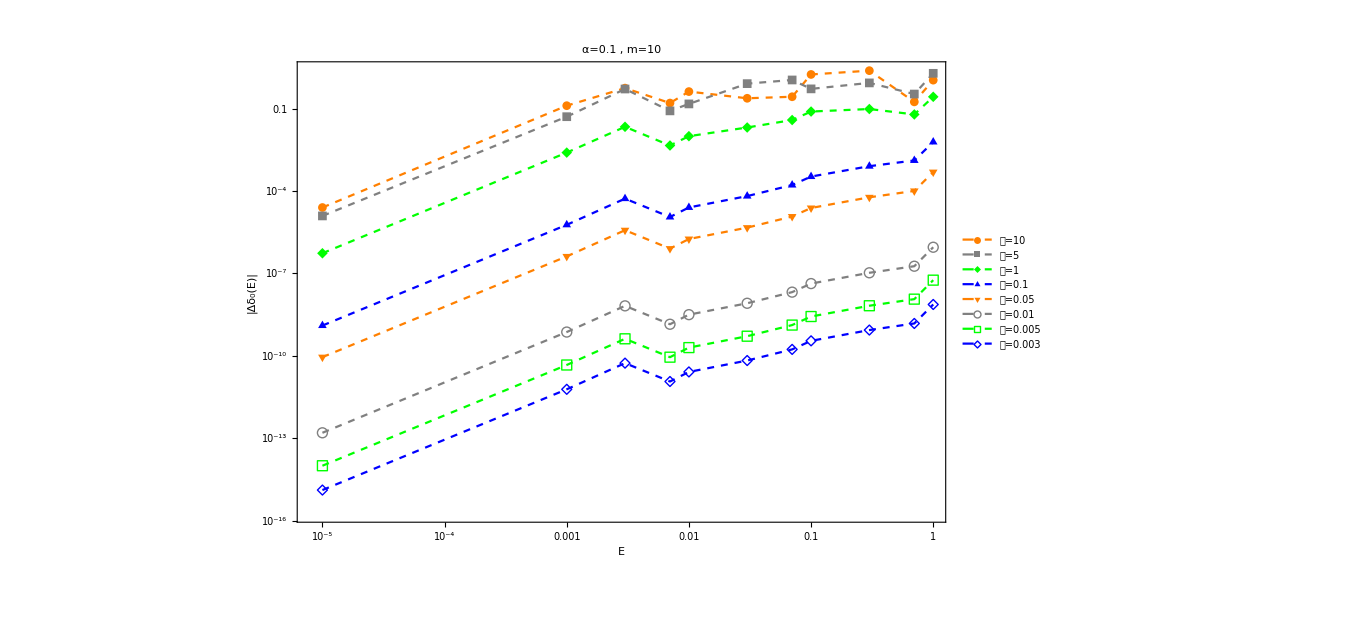

```mathematica
ListLogLogPlot[Table[Drop[La[[n]],1],{n,Length@aa}],Frame->True,Joined->True,PlotMarkers->Automatic,ImageSize->1000,FrameLabel->{"E","|Δδ_0(E)|"},RotateLabel->False,PlotStyle->{{Dashed,Orange},{Dashed,Gray},{Dashed,Green},{Dashed,Blue}},PlotLegends->(("𝒶="<>ToString[#])&/@aa),PlotLabel->Style[("α="<>ToString@α<>" ,  m="<>ToString@m),20]]
Export["C:\\Users\\ASUS\\OneDrive\\文档\\Test_6\\Test_Coulomb_3_Various_a_1.eps",%];
```

```mathematica
a=;
```

## Calculating eigenenergy of Coulomb Potential

```mathematica
EigenEnergy[V[r],αSch]
```

## Determine 𝒸_1 in V_eff^(a^2)

```mathematica
hhhc[en_,c1_?NumberQ]:=δ50e[en,Vs1[r,a,c1]];
evnhhhc[c1_]:=N[hhhc[10^-10,c1]-δ50e[10^-10,V[r]],8];
Determinec1:=Module[{aaa,findroot},aaa=a;
Print[a];findroot=FindRoot[hhhc1[10^-10,aaa,c1]==δ50e[10^-10,V[r]],{c1,-40},MaxIterations->10000,AccuracyGoal->30,PrecisionGoal->30,WorkingPrecision->80,StepMonitor:>Print[{c1,evnhhhc1[aaa,c1]}]];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
c1=Determinec1
```

```mathematica
energyVs1=EigenEnergy[Vs1[r,a,c1],αSch]
```

```mathematica
δVs1=δ50[Vs1[r,a,c1]]
```

## Determine 𝒸_2 and 𝒹_1 in V_eff^(a^4)

```mathematica
hhh[en_,c2_?NumberQ,d1_?NumberQ]:=δ50e[en,Vs2[r,a,c2,d1]]
evnhhh1:=N[hhh[ee[[1]],c2,d1]-δ50e[ee[[1]],V[r]],8];
evnhhh2:=N[hhh[ee[[2]],c2,d1]-δ50e[ee[[2]],V[r]],8];
```

```mathematica
Determinec2d1:=Module[{findroot},
findroot=FindRoot[{hhh[ee[[1]],c2,d1]==δ50e[ee[[1]],V[r]],hhh[ee[[2]],c2,d1]==δ50e[ee[[2]],V[r]]},{{c2,-40.},{d1,3.}},MaxIterations->10000,AccuracyGoal->12,WorkingPrecision->50,StepMonitor:>Print[{c2,d1,evnhhh1,evnhhh2}]];
{c2,d1}/.findroot
]
```

```mathematica
{c2,d1}=Determinec2d1
```

```mathematica
energyVs2=EigenEnergy[Vs2[r,a,{c2,d1}],αSch]
```

```mathematica
δVs2=δ50[Vs2[r,a,{c2,d1}]]
```

## Matrix element <p^4>

```mathematica
nRange=20;
```

```mathematica
p4Ture[n_,b_][Z_,γ_,η_,opt___]:=Z NIntegrate[(Laplacian[efVs2[[n]],{r}]^2),{r,0,b},opt]+γ/a NIntegrate[efVs2[[n]]^2 δa[r],{r,0,b},opt]+η a NIntegrate[efVs2[[n]]^2 Laplacian[δa[r],{r,θ,ϕ},"Spherical"],{r,0,b},opt]
```

```mathematica
REAL=Table[Integrate[D[r RS[n,r],{r,2}]^2,{r,0,∞}],{n,nRange}];
REF=Table[Integrate[D[r RS[n,r],{r,2}]^2,{r,0,∞}],{n,nRange-2,nRange}];
```

### Matrix element in V_eff^(a^2)

```mathematica
efVs1=Module[{ef,am},
ef=Eigenfun[Vs1[r,a,c1],energyVs1];
am=NIntegrate[f[r]^2/.#,{r,1.*10^-50,2000}]^-0.5&/@ef;
(am[[2#]]=-am[[2#]])&@Range@10;
Table[am[[n]]f[r]/.ef[[n]],{n,20}]
]
```

```mathematica
AbsoluteTiming@GraphicsGrid@Partition[Table[Plot[{(RS[n,r]r),efVs1[r]},{r,0,2000},PlotRange->Full,ImageSize->Medium,PlotStyle->{Blue,Orange}],{n,20}],4]
AbsoluteTiming@GraphicsGrid@Partition[Table[Plot[(RS[n,r]r)-efVs1[r],{r,0,2000},PlotRange->Full,ImageSize->Medium],{n,20}],4]
```

```mathematica
FALSEVs1=NIntegrate[D[efVs1[[#]],{r,2}]^2,{r,0,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange
N[%,6]
Abs@((REAL-FALSEVs1)/REAL);
N[%,6]
```

```mathematica
RESVs1=FindRoot[Evaluate@Thread[(p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@{10,15,20})==(REF[[#]]&/@{1,2,3})](*/.Z->1*),{{Z,1.1,1.12},{γ,0,100},{η,100,-2}},WorkingPrecision->50,AccuracyGoal->6,PrecisionGoal->6]
```

```mathematica
p4Vs1=p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange/.RESVs1;
N[%,6]
Abs[(p4Vs1-REAL)/REAL];
N[%,6]
```

### Matrix element in V_eff^(a^4)

```mathematica
efVs2=Module[{ef,am},
ef=Eigenfun[Vs2[r,a,c1],energyVs2];
am=NIntegrate[f[r]^2/.#,{r,1.*10^-50,2000}]^-0.5&/@ef;
(am[[2#]]=-am[[2#]])&@Range@10;
Table[am[[n]]f[r]/.ef[[n]],{n,20}]
]
```

```mathematica
AbsoluteTiming@GraphicsGrid@Partition[Table[Plot[{(RS[n,r]r),efVs1[r]},{r,0,2000},PlotRange->Full,ImageSize->Medium,PlotStyle->{Blue,Orange}],{n,20}],4]
AbsoluteTiming@GraphicsGrid@Partition[Table[Plot[(RS[n,r]r)-efVs1[r],{r,0,2000},PlotRange->Full,ImageSize->Medium],{n,20}],4]
```

```mathematica
FALSEVs2=NIntegrate[D[efVs2[[#]],{r,2}]^2,{r,0,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange
N[%,6]
Abs@((REAL-FALSE)/REAL);
N[%,6]
```

```mathematica
RESVs2=FindRoot[Evaluate@Thread[(p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@{10,15,20})==(REF[[#]]&/@{1,2,3})](*/.Z->1*),{{Z,1.1,1.12},{γ,0,100},{η,100,-2}},WorkingPrecision->50,AccuracyGoal->6,PrecisionGoal->6]
```

```mathematica
p4Vs2=p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange/.RESVs2;
N[%,6]
Abs[(p4Vs2-REAL)/REAL];
N[%,6]
```